```mathematica
SDATA={
CI ->  1.5 10^6,(*Pa*)
TW-> 0.170, (*m*)
TL ->  1.500 , (*m*)
(*W->  939.9 9.81 ,N*)
DWR -> 1,
v->2.0 (*m/s*),
IF->16816.74308640379(*N*),
r-> 0.740/2
};
Wnom =9.81 3000.0;(*9.81 939.9*)
Bn = (CI TW TL)/(W (1-Exp[-CI/(0.698 10^6)]))5/(1+6 TW/TL);
DWI = 1 - Abs[(0.7(DWR-1))/(DWR+1)];
GTR = 1.10 (1-Exp[-0.025 Bn])(1-Exp[-17 s])+0.03/DWI;
MRR=2.5/(Bn DWI)+0.03/DWI+(0.5s)/(√Bn);
NTR = GTR - MRR;
TE = NTR/GTR(1-s);
GT = W GTR;
MR = W MRR;
NT = W NTR;
H = NT v/(TE 735.5) ;(*cv*)
```

```mathematica
Wnom/9.81
```

3000.

```mathematica
si =s/. FindRoot[({NT-IF/.SDATA/.W->Wnom})== 0,{s,0.01}]
```

0.120558

```mathematica
Bn/.SDATA/.W->Wnom
```

43.787

```mathematica
sy = ((1-sx)x)/R;
σ=√(sx^2+sy^2);
```

```mathematica
dFydx[R_]=sy/σ W/TL GTR//.{s->σ,W->Wnom,sx->si}//.SDATA;
```

```mathematica
dFydx[10]
```

(1725.46 (0.03+0.731887 (1-ⅇ^(-17 √(0.0145343+0.00773418 x^2)))) x)/(√(0.0145343+0.00773418 x^2))

```mathematica
TLn=TL//.SDATA;
```

```mathematica
Fy[R_]:=NIntegrate[dFydx[R] ,{x,-TLn/2,TLn/2}];
```

```mathematica
Fy2[R_]:=NIntegrate[dFydx[R] ,{x,0,TLn/2}];
```

```mathematica
M[R_]:=NIntegrate[x dFydx[R] ,{x,-TLn/2,TLn/2}];
```

General::munfl: Exp[-11212.4] is too small to represent as a normalized machine number; precision may be lost.

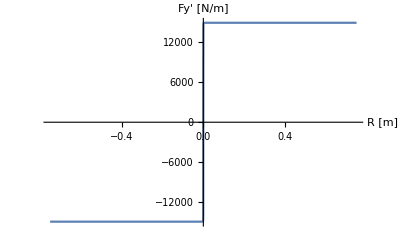

```mathematica
Plot[dFydx[0.001],{x,-TLn/2,TLn/2},AxesLabel->{"R [m]","Fy' [N/m]"},PlotRange->{-15000,15000}]
```

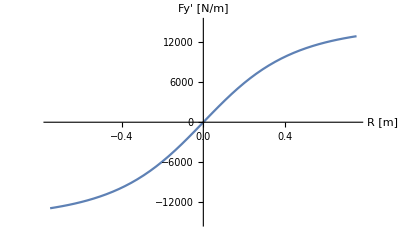

```mathematica
Plot[dFydx[3],{x,-TLn/2,TLn/2},AxesLabel->{"R [m]","Fy' [N/m]"},PlotRange->{-15000,15000}]
```

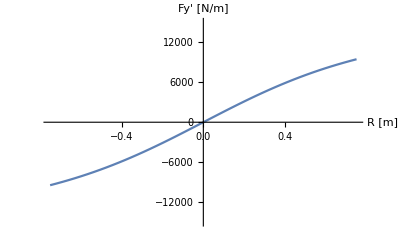

```mathematica
Plot[dFydx[6],{x,-TLn/2,TLn/2},AxesLabel->{"R [m]","Fy' [N/m]"},PlotRange->{-15000,15000}]
```

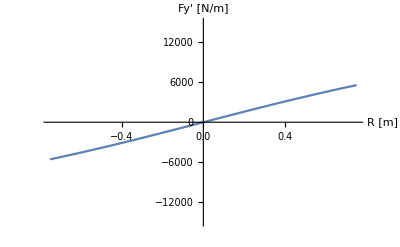

```mathematica
Plot[dFydx[12],{x,-TLn/2,TLn/2},AxesLabel->{"R [m]","Fy' [N/m]"},PlotRange->{-15000,15000}]
```

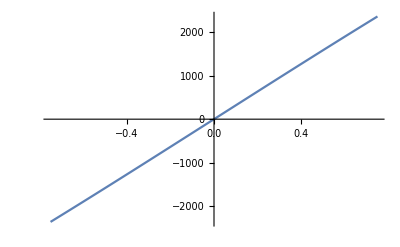

```mathematica
Plot[dFydx[30],{x,-TLn/2,TLn/2}]
```

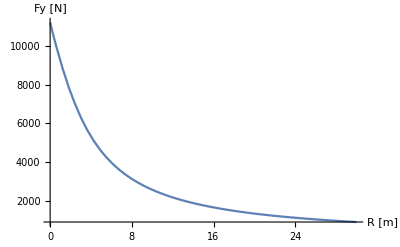

```mathematica
Plot[Fy2[R],{R,0,30},AxesLabel->{"R [m]","Fy [N]"},PlotRange->All]
```

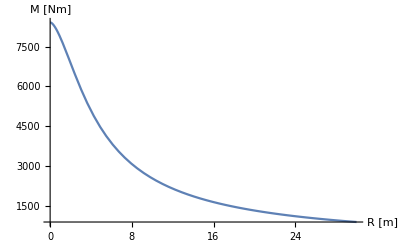

```mathematica
Plot[M[R],{R,0,30},AxesLabel->{"R [m]","M [Nm]"}]
```

```mathematica
M[2]+M[4]
```

11963.7

```mathematica
Fy2[3]
```

6307.95

```mathematica
W/TL GTR/.s->σ
```

(W (1.1 (1-ⅇ^(-(0.125 CI TL TW)/((1-ⅇ^(-1.43266×10^-6 CI)) (1+(6 TW)/TL) W))) (1-ⅇ^(-17 √(sx^2+((1-sx)^2 x^2)/R^2)))+0.03/(1-0.7 Abs[(-1+DWR)/(1+DWR)])))/TL

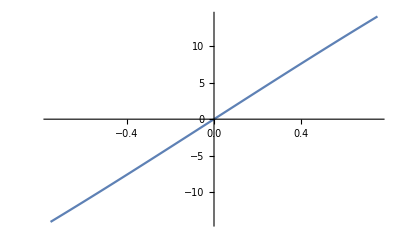

```mathematica
Plot[180/π ArcTan[x/3],{x,-TLn/2,TLn/2}]
```

```mathematica
2M[0.0001]
```

16816.7